## Standard Halo model, in Earth frame

* vl : Local standard of rest (LSR) galactic velocity (i.e., sun velocity)
	(We can for now assume earth velocity averages to sun’s velocity)
* vesc : galactic escape velocity
* vc : Galactic disk circular orbit velocity
* θ : polar angle of the DM particle velocity with respect to Earth’s motion
* K : Normalisation constant, accounting for escape velocity
* ve[θ] : escape velocity from local frame, as function of theta
* F[v,θ] : Full vector standard halo model
* f[v,θ] : vector SHM, ignoring escape velocity cut-off
* Fg[v] : galactic SHM

```mathematica
vc=220.0;
vl = 220.0;
vesc = 544.0;
ve[θ_]:=√(vesc^2-vl^2 Sin[θ]^2)-vl Cos[θ]
K = -2 vesc/(√π vc)Exp[-vesc^2/vc^2]+Erf[vesc/vc];
Fg[v_]:=1/(K π^(3/2))1/vc^3 Exp[(-(v^2))/vc^2]HeavisideTheta[vesc-v]
F[v_,θ_]:=1/(K π^(3/2))1/vc^3 Exp[(-(v^2+vl^2+2 v vl Cos[θ]))/vc^2]HeavisideTheta[ve[θ]-v]
f[v_,θ_]:=1/(K π^(3/2))1/vc^3 Exp[(-(v^2+vl^2+2 v vl Cos[θ]))/vc^2]
```

```mathematica
Integrate[Sin[θ],{θ,0,π}]
```

2

#### Check normalisation:

```mathematica
2π NIntegrate[v^2 F[v,θ]Sin[θ],{θ,0,π},{v,0,ve[θ]}]
2π NIntegrate[ v^2 F[v,θ]Sin[θ],{θ,0,π},{v,0,999.0}]//Quiet
4π Integrate[v^2 Fg[v],{v,0,vesc}]
```

1.

1.

1.

```mathematica
fv[v_]:=Integrate[2π f[v,θ]Sin[θ],{θ,0,π}]
```

```mathematica
Integrate[fv[v] v^2,{v,0,vesc}]
Integrate[fv[v] v^2,{v,0,10*vesc}]
```

0.955464

1.00668

#### Mean speed in local frame

```mathematica
NIntegrate[v 2π v^2 F[v,θ]Sin[θ],{θ,0,π},{v,0,ve[θ]}]
NIntegrate[v 2π v^2 F[v,θ]Sin[θ],{θ,0,π},{v,0,999.0}]//Quiet
```

321.802

321.802

```mathematica
Integrate[v fv[v] v^2,{v,0,vesc}]
Integrate[v fv[v] v^2,{v,0,vesc +0.5*vl}]
Integrate[v fv[v] v^2,{v,0,10*vesc}]
```

294.928

319.975

325.917

## Speed and angular distributions

```mathematica
Fv[v_]:=v^2 2π NIntegrate[ F[v,θ]Sin[θ],{θ,0,π}]
fv[v_]:=v^2 2π NIntegrate[ f[v,θ]Sin[θ],{θ,0,π}]
```

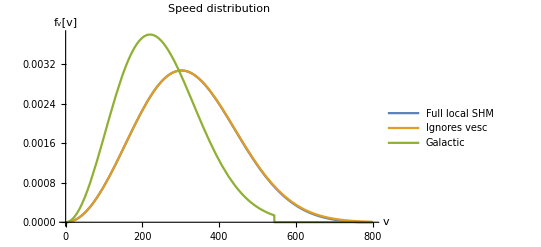

```mathematica
Plot[{Fv[v],fv[v],4π v^2 Fg[v]},{v,0.0,800.0},PlotLegends->{"Full local SHM","Ignores vesc","Galactic"}, PlotLabel->"Speed distribution",AxesLabel->{"v","f_v[v]"}]
```

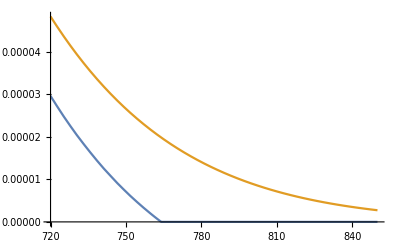

```mathematica
Plot[{Fv[v],fv[v]},{v,720,850}]//Quiet
```

```mathematica
Fθ[θ_]:=Sin[θ]2π NIntegrate[v^2 F[v,θ],{v,0,ve[θ]}]
fθ[θ_]:=Sin[θ]2π NIntegrate[v^2 f[v,θ],{v,0,vesc }]
fgθ[θ_]:=Sin[θ]2π NIntegrate[v^2 Fg[v],{v,0,vesc }]
```

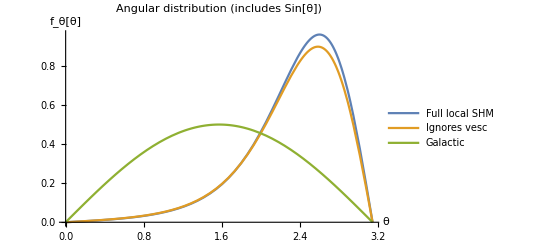

```mathematica
Plot[{Fθ[θ],fθ[θ],fgθ[θ]},{θ,0,π},PlotLegends->{"Full local SHM","Ignores vesc","Galactic"}, PlotLabel->"Angular distribution (includes Sin[θ])",AxesLabel->{"θ","f_θ[θ]"}]
```

## Average

∫d^3 v F(v,θ)v .D = 2π D∫dv dθ v^2 v Cosθ Sinθ

```mathematica
2π NIntegrate[ v^3 F[v,θ]Sin[θ]Cos[θ],{θ,0,π},{v,0,999.0}]//Quiet
```

-220.